```mathematica
a=.77;
```

```mathematica
b=1.1;
```

```mathematica
c=0;
```

```mathematica
d=3.7;
```

```mathematica
A=StreamPlot[{a y-x y-b x,c+d x-y+x y},{x,-1,1},{y,-1,2},StreamStyle->Black];
```

```mathematica
B=Plot[{(b x)/(a-x),(d x+c)/(1-x)},{x,-1,2}];
```

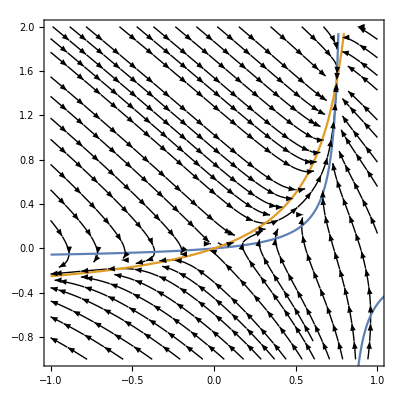

```mathematica
Show[A,B]
```

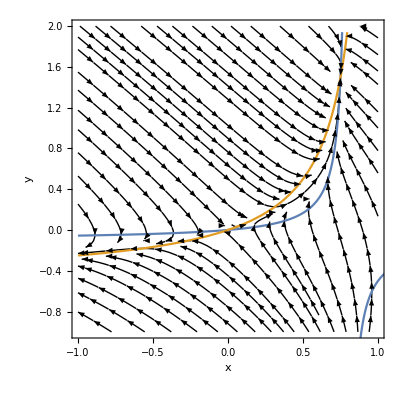

```mathematica
Show[Show[A,B],FrameLabel->{{HoldForm[y],None},{HoldForm[x],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
plo3=ContourPlot[{(2*(d-b)*y-a*d+b+x)^2==(b+x-a*d)^2+4a*x*(d-b),y==1/(2*(d-b))*(Sqrt[(x^2+4a*x*(d-b))]-x)},{x,-5,50},{y,0,1},PlotLegends->"Expressions",Axes->True,FrameLabel->{{HoldForm[x],None},{HoldForm[c],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```